# DarkMode Theme

## Chapter 01 全局选项声明

## 声明选项

1. 文档背景

2. Plot的label的颜色

3. 语法高亮

```mathematica
SetOptions[
	EvaluationNotebook[],
	Background->RGBColor[255,255,255]
];
```

```mathematica
(* 笔记本背景 *)
SetOptions[
	EvaluationNotebook[],
	Background->RGBColor[0,0,0]
];


(* 绘图label设置 *)
SetOptions[
	{Plot, Plot3D}, {LabelStyle -> White}
];


(* 语法高亮设置 *)
SetOptions[
	EvaluationNotebook[],                                                        (* 1.Only Apply to Current Notebook *)
	Background->RGBColor[0, 0, 0],                                                                      (* 2.背景颜色设置 *)
	AutoStyleOptions -> {
	"LocalVariableStyle" -> {FontColor-> RGBColor[0, 1, 0.25098]},         (* 3.局部变量颜色 *)
	"StringStyle"->{FontColor->RGBColor[0.86, 0.56, 0.06]},                            (* 4.字符串颜色 *)
	"CommentStyle"->{
		FontColor->RGBColor[0.5019607843137255, 1., 0.5019607843137255],
		ShowAutoStyles->False,ShowSyntaxStyles->False,
		AutoNumberFormatting->False,
		TranslationOptions->{"Enabled"->False}
	},                                                                                                                                    (* 5.注释颜色 *)
	"FunctionLocalVariableStyle"->{FontColor->RGBColor[0.6196078431372549, 0.6196078431372549, 0.6196078431372549]},                                   (* 6.函数中局部变量的颜色 *)
	"PatternVariableStyle"->{FontColor->RGBColor[0.5019607843137255, 0.5019607843137255, 1.],FontSlant->"Italic"}, (* 7.模式匹配变量的颜色 *)
         "UndefinedSymbolStyle"->{FontColor->RGBColor[0.93, 0.62, 0.46]}                                                    (* 8.未赋值的全局符号的颜色 *)
      }
];

(* 使用下面的命令获取当前高亮参数 *)
(*Options[Notebook, AutoStyleOptions]*)


(*备注:匹配的函数头需要单独手动设置语法高亮为: RGB(128, 128, 192)*)
```

## Chapter 02 测试模板

```mathematica
fun1[x_, y_, t_] :=Module[
	{xtemp, ytemp}, 
          xtemp = x+1;
        ytemp = xtemp ^2;
       temp = xtemp* ytemp
]
```

```mathematica
fun1[1, 2, 2]
```

8

```mathematica
RGBColor[0,1,0.25098]
RGBColor[0., 1., 0.25098039215686274]//FullForm
RGBColor[2/3,2/3,1]
RGBColor[0.86, 0.56, 0.06]//FullForm
```

RGBColor[0, 1, 0.25098]

RGBColor[0.,1.,0.25098]

RGBColor[Rational[2, 3], Rational[2, 3], 1]

RGBColor[0.86,0.56,0.06]

```mathematica
Series[Exp[x], {x, 0, 10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

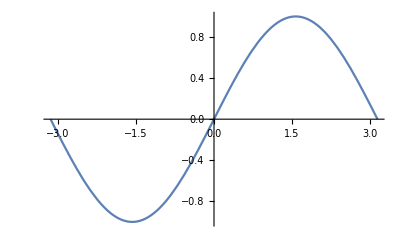

```mathematica
fp1 = Plot[Sin[x], {x, -Pi, Pi}];
fp2 = Plot3D[Sin[x*y], {x, -Pi, Pi}, {y, -Pi, Pi}];
GraphicsRow[{fp1, fp2}]
```

```mathematica
Hello
```

Item 1

Item 2

## Section

### SubSection

#### Subsubsection